```mathematica
(* 基本和描述统计 *)
popSelect[x_]:=QuantityMagnitude[CountryData[x,"Population"]]>=5*10^6;(* 定义人口数量大于5*10^6 的国家为大国 *)
largeCountry  = Select[CountryData[All],popSelect];
```

```mathematica
LargeCountriesCellAndInternet = Table[
	{CountryData[i,"CellularPhones"],CountryData[i,"InternetUsers"]},
	{i,largeCountry}
];
```

```mathematica
Dimensions[LargeCountriesCellAndInternet](* 使用Dimensions查看数据集的大小 *)
```

{122,2}

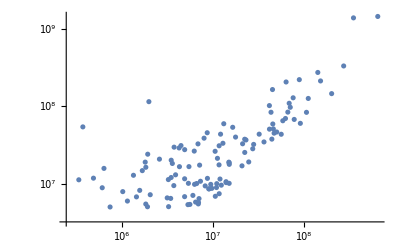

```mathematica
ListLogLogPlot[Table[Tooltip[{CountryData[i,"CellularPhones"],CountryData[i,"Population"]},i],{i,largeCountry}]]
```

```mathematica
(* 删除原始数据集中的缺失值 *)
LargeCountriesCellAndInternet = Cases[
	 Table[
	{CountryData[i,"CellularPhones"],CountryData[i,"InternetUsers"]},
	{i,largeCountry}
],
{_Real,_Quantity}
];
```

```mathematica
Dimensions[LargeCountriesCellAndInternet]
```

{118,2}

```mathematica
(* Head用于展示大规模数据集中的底层数据的标头 *)
Head[LargeCountriesCellAndInternet[[1,1]]]
```

Real

```mathematica
Head[LargeCountriesCellAndInternet[[1,2]]]
```

Quantity

```mathematica
(* FullForm用于返回符号的底层表示 *)
FullForm[{1,2,3}]
```

List[1,2,3]

```mathematica
Mean[LargeCountriesCellAndInternet]
```

{3.32212×10^7,1.30537×10^7 people}

```mathematica
Mean[LargeCountriesCellAndInternet[[All,1]]]
```

3.32212×10^7

```mathematica
Total[LargeCountriesCellAndInternet[[All,1]]]
```

3.92011×10^9

```mathematica
Manipulate[
function[LargeCountriesCellAndInternet[[All,1]]],
{function,{Mean,HarmonicMean,GeometricMean,Median,Variance,Total,StandardDeviation,InterquartileRange,Max,Min,Accumulate}},
SaveDefinitions->True
]
```

```mathematica
(* 计算协方差 *)
Covariance[LargeCountriesCellAndInternet[[All,1]],LargeCountriesCellAndInternet[[All,2]]]
```

2.46803×10^15 people

```mathematica
(* 求解相关系数 *)
Correlation[LargeCountriesCellAndInternet[[All,1]],LargeCountriesCellAndInternet[[All,2]]]
```

0.88948

```mathematica
(* 曲线拟合 *)
QuantityMagnitude[LargeCountriesCellAndInternet]
```

{{7.89891×10^6,500000.},{3.1871×10^7,4.1×10^6},{6.77336×10^6,550000.},{4.65088×10^7,1.12122×10^7},{2.212×10^7,1.517×10^7},{1.0816×10^7,5.93667×10^6},{6.548×10^6,2.44455×10^6},{4.464×10^7,556000.},{8.128×10^6,3.1069×10^6},{1.18222×10^7,7.29225×10^6},{3.435×10^6,160000.},{4.83×10^6,1.05×10^6},{1.50641×10^8,7.20277×10^7},{1.05002×10^7,2.64706×10^6},{2.553×10^6,140000.},{480584.,65000.},{4.237×10^6,74000.},{6.16089×10^6,725000.},{2.20925×10^7,2.5086×10^7},{1.809×10^6,130000.},{1.47966×10^7,5.45624×10^6},{6.4123×10^8,2.98×10^8},{4.13647×10^7,1.73297×10^7},{1.88657×10^6,1.46×10^6},{331736.,1.45×10^6},{1.37802×10^7,6.02775×10^6},{6.862×10^6,4.57862×10^6},{7.21048×10^6,2.14739×10^6},{1.15421×10^7,3.882×10^6},{4.12725×10^7,1.3573×10^7},{6.9507×10^6,650000.},{1.95453×10^6,360000.},{6.83×10^6,4.3827×10^6},{5.7972×10^7,4.23154×10^7},{1.05523×10^8,6.19731×10^7},{1.15704×10^7,997000.},{1.37993×10^7,4.84461×10^6},{1.49486×10^7,1.96×10^6},{3.84039×10^6,90000.},{3.2×10^6,1.×10^6},{6.21071×10^6,958000.},{1.15801×10^7,4.67813×10^6},{1.22242×10^7,5.87315×10^6},{3.4689×10^8,5.175×10^7},{1.40578×10^8,1.8×10^7},{4.3×10^7,2.3×10^7},{1.7529×10^7,300000.},{8.982×10^6,3.5×10^6},{9.0341×10^7,2.49915×10^7},{1.0449×10^7,660000.},{1.10395×10^8,9.5979×10^7},{5.31356×10^6,1.59525×10^6},{1.49106×10^7,1.707×10^6},{1.63036×10^7,3.35955×10^6},{3.39402×10^6,850000.},{2.02213×10^6,527450.},{1.427×10^6,945000.},{732000.,20000.},{4.828×10^6,323000.},{4.83524×10^6,316100.},{1.781×10^6,316100.},{2.7713×10^7,1.5074×10^7},{3.43901×10^6,200000.},{7.53053×10^7,2.35674×10^7},{2.28157×10^7,1.04425×10^7},{4.40501×10^6,350000.},{367388.,108855.},{4.2×10^6,499000.},{2.0627×10^7,1.43046×10^7},{3.108×10^6,185000.},{1.89763×10^6,80000.},{6.29885×10^7,2.39822×10^7},{5.25089×10^6,3.93482×10^6},{3.21935×10^6,557000.},{8.80197×10^7,1.85×10^7},{600000.,120000.},{5.95439×10^6,894212.},{2.09518×10^7,7.12835×10^6},{6.81172×10^7,5.618×10^6},{4.39264×10^7,1.86791×10^7},{1.49096×10^7,4.47574×10^6},{1.807×10^6,155000.},{2.4467×10^7,6.19477×10^6},{1.99522×10^8,4.525×10^7},{1.32264×10^6,300000.},{3.6×10^7,7.76176×10^6},{5.38913×10^6,1.02×10^6},{9.61877×10^6,3.3×10^6},{1.0088×10^6,13900.},{6.3755×10^6,3.37×10^6},{5.52004×10^6,3.56647×10^6},{627000.,102000.},{4.5×10^7,4.187×10^6},{4.5607×10^7,3.6837×10^7},{4.96775×10^7,2.524×10^7},{1.10825×10^7,1.16349×10^6},{1.19915×10^7,4.2×10^6},{1.0892×10^7,8.0855×10^6},{8.89671×10^6,5.8068×10^6},{7.05616×10^6,3.565×10^6},{3.67352×10^6,600000.},{1.30068×10^7,520000.},{6.2×10^7,1.61×10^7},{1.54954×10^6,350000.},{8.60216×10^6,2.8×10^6},{6.58241×10^7,2.54054×10^7},{1.13515×10^6,75000.},{8.55486×10^6,2.5×10^6},{5.56945×10^7,4.87519×10^6},{9.35774×10^6,2.922×10^6},{7.73608×10^7,4.66839×10^7},{2.705×10^8,2.3063×10^8},{1.27337×10^7,2.469×10^6},{2.70838×10^7,7.16738×10^6},{7.×10^7,2.0834×10^7},{3.7×10^6,370000.},{3.539×10^6,700000.},{1.65472×10^6,1.421×10^6}}

```mathematica
fit1 = Fit[QuantityMagnitude[LargeCountriesCellAndInternet],{1,x},x]
```

-1.36023×10^6+0.433878 x

```mathematica
(* 曲线拟合的结果可以被直接用来绘图 *)
fit1
```

-1.36023×10^6+0.433878 x

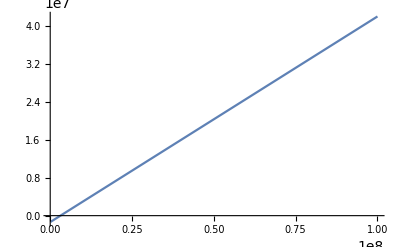

```mathematica
Plot[fit1,{x,10^5,10^8}]
```

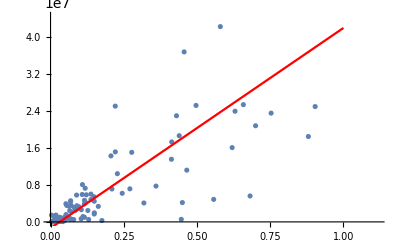

```mathematica
Show[
	{
	ListPlot[LargeCountriesCellAndInternet],
	Plot[fit1,{x,10^5,10^8},PlotStyle->Red]
}
]
```

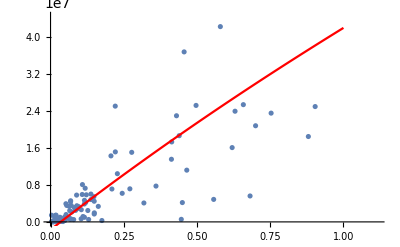

```mathematica
(* 使用Fit进行对高阶多项式的拟合 *)
fit2 = Fit[LargeCountriesCellAndInternet,{1,x,x^2,x^3},x];
Show[
	{
ListPlot[LargeCountriesCellAndInternet],
Plot[fit2,{x,10^5,10^8},PlotStyle->Red]
}
]
```

```mathematica
x^Range[4]
```

{x,x^2,x^3,x^4}

```mathematica
(* 使用Manipulate来操纵不同的拟合次数 *)
Manipulate[
	fit3 =Fit[LargeCountriesCellAndInternet[[All,1]],x^Range[degree],x];
	Show[{
	ListPlot[LargeCountriesCellAndInternet[[All,1]]],
	Plot[fit3,{x,0,150},PlotStyle->Red]
}],{degree,1,6,1}
]
```

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

Fit::fitd: Fit 中的第一个参数 Symbol[] 不是一个列表，也不是一个矩形数组.

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

ListPlot::lpn: Symbol[] 不是由数字或者数对组成的列表.

General::ivar: 0.00306429 不是一个有效的变量.

General::ivar: 3.06429 不是一个有效的变量.

General::ivar: 6.12551 不是一个有效的变量.

General::stop: 在本次计算中，General::ivar 的进一步输出将被抑制.

Show::gcomb: 无法合并 Show[{ListPlot[Symbol[]],}] 中的图形对象.

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

Fit::fitd: Fit 中的第一个参数 Symbol[] 不是一个列表，也不是一个矩形数组.

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

ListPlot::lpn: Symbol[] 不是由数字或者数对组成的列表.

General::ivar: 0.00306429 不是一个有效的变量.

General::ivar: 3.06429 不是一个有效的变量.

General::ivar: 6.12551 不是一个有效的变量.

General::stop: 在本次计算中，General::ivar 的进一步输出将被抑制.

Show::gcomb: 无法合并 Show[{ListPlot[Symbol[]],}] 中的图形对象.

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

Fit::fitd: Fit 中的第一个参数 Symbol[] 不是一个列表，也不是一个矩形数组.

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

ListPlot::lpn: Symbol[] 不是由数字或者数对组成的列表.

General::ivar: 0.00306429 不是一个有效的变量.

General::ivar: 3.06429 不是一个有效的变量.

General::ivar: 6.12551 不是一个有效的变量.

General::stop: 在本次计算中，General::ivar 的进一步输出将被抑制.

Show::gcomb: 无法合并 Show[{ListPlot[Symbol[]],}] 中的图形对象.

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

Fit::fitd: Fit 中的第一个参数 Symbol[] 不是一个列表，也不是一个矩形数组.

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

ListPlot::lpn: Symbol[] 不是由数字或者数对组成的列表.

General::ivar: 0.00625625 不是一个有效的变量.

General::ivar: 6.25626 不是一个有效的变量.

General::ivar: 12.5063 不是一个有效的变量.

General::stop: 在本次计算中，General::ivar 的进一步输出将被抑制.

Show::gcomb: 无法合并 Show[{ListPlot[Symbol[]],}] 中的图形对象.

```mathematica
LargeCountriesCellAndInternet[[All,1]]
```

{7.89891×10^6,3.1871×10^7,6.77336×10^6,4.65088×10^7,2.212×10^7,1.0816×10^7,6.548×10^6,4.464×10^7,8.128×10^6,1.18222×10^7,3.435×10^6,4.83×10^6,1.50641×10^8,1.05002×10^7,2.553×10^6,480584.,4.237×10^6,6.16089×10^6,2.20925×10^7,1.809×10^6,1.47966×10^7,6.4123×10^8,4.13647×10^7,1.88657×10^6,331736.,1.37802×10^7,6.862×10^6,7.21048×10^6,1.15421×10^7,4.12725×10^7,6.9507×10^6,1.95453×10^6,6.83×10^6,5.7972×10^7,1.05523×10^8,1.15704×10^7,1.37993×10^7,1.49486×10^7,3.84039×10^6,3.2×10^6,6.21071×10^6,1.15801×10^7,1.22242×10^7,3.4689×10^8,1.40578×10^8,4.3×10^7,1.7529×10^7,8.982×10^6,9.0341×10^7,1.0449×10^7,1.10395×10^8,5.31356×10^6,1.49106×10^7,1.63036×10^7,3.39402×10^6,2.02213×10^6,1.427×10^6,732000.,4.828×10^6,4.83524×10^6,1.781×10^6,2.7713×10^7,3.43901×10^6,7.53053×10^7,2.28157×10^7,4.40501×10^6,367388.,4.2×10^6,2.0627×10^7,3.108×10^6,1.89763×10^6,6.29885×10^7,5.25089×10^6,3.21935×10^6,8.80197×10^7,600000.,5.95439×10^6,2.09518×10^7,6.81172×10^7,4.39264×10^7,1.49096×10^7,1.807×10^6,2.4467×10^7,1.99522×10^8,1.32264×10^6,3.6×10^7,5.38913×10^6,9.61877×10^6,1.0088×10^6,6.3755×10^6,5.52004×10^6,627000.,4.5×10^7,4.5607×10^7,4.96775×10^7,1.10825×10^7,1.19915×10^7,1.0892×10^7,8.89671×10^6,7.05616×10^6,3.67352×10^6,1.30068×10^7,6.2×10^7,1.54954×10^6,8.60216×10^6,6.58241×10^7,1.13515×10^6,8.55486×10^6,5.56945×10^7,9.35774×10^6,7.73608×10^7,2.705×10^8,1.27337×10^7,2.70838×10^7,7.×10^7,3.7×10^6,3.539×10^6,1.65472×10^6}

```mathematica
(* FindFit *)
fit4 = FindFit[LargeCountriesCellAndInternet[[All,1]],a Log[x]+b,{a,b},x] (* 指定数据集 拟合待定方程 系数 自编量 *)
```

{a→-530060.,b→3.52348×10^7}

```mathematica
ReplaceAll[a Log[x] + b,fit4]
```

3.52348×10^7-530060. Log[x]

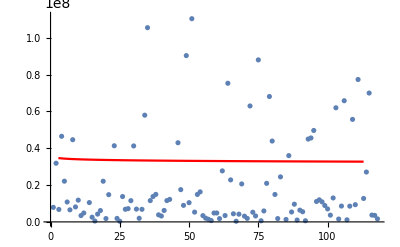

```mathematica
Show[{
ListPlot[LargeCountriesCellAndInternet[[All,1]]],
Plot[ReplaceAll[a Log[x] + b,fit4],{x,0,113},PlotStyle->Red]
}]
```

```mathematica
(* 构建统计模型 *)
```

```mathematica
model = LinearModelFit[QuantityMagnitude[LargeCountriesCellAndInternet],{1,x,x^2},x]
```

FittedModel[-352568.+0.381453 x+1.08838×10^-10 x^2]

```mathematica
Normal[%]
```

-352568.+0.381453 x+1.08838×10^-10 x^2

```mathematica
model[10^7](* 模型的使用 *)
```

3.47285×10^6

```mathematica
Table[model[i],{i,10^6,10^7,10^6}]
```

{28993.7,410773.,792770.,1.17499×10^6,1.55742×10^6,1.94007×10^6,2.32294×10^6,2.70602×10^6,3.08932×10^6,3.47285×10^6}

```mathematica
∫model[x]ⅆx
```

-352568. x+0.190727 x^2+3.62794×10^-11 x^3

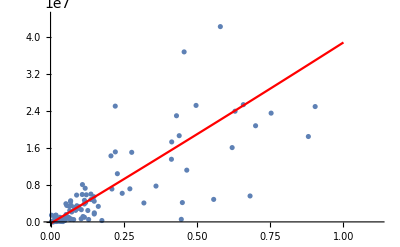

```mathematica
Show[ListPlot[LargeCountriesCellAndInternet],Plot[model[x],{x,10^5,10^8},PlotStyle->Red]]
```

```mathematica
(* 显示可用统计属性 *)
Short[model["Properties"],10]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,«4»,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
model["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 1.25287×10^17 | 1.25287×10^17 | 440.789 | 3.78309×10^-41
x^2 | 1 | 3.81825×10^14 | 3.81825×10^14 | 1.34335 | 0.248845
Error | 115 | 3.26868×10^16 | 2.84233×10^14 |  | 
Total | 117 | 1.58355×10^17 |  |  |

```mathematica
Short[model["FitResiduals"],5]
```

{-2.16729×10^6,-7.81527×10^6,-1.68614×10^6,-6.41162×10^6,7.03157×10^6,2.15071×10^6,294697.,-1.63364×10^7,351828.,3.12×10^6,-799007.,-442389.,1.24478×10^7,-1.0177×10^6,-481991.,234223.,«87»,111229.,-136807.,177538.,-5578.51,-418676.,-1.63547×10^7,-304499.,1.68756×10^7,1.19836×10^8,-2.0534×10^6,-2.89111×10^6,-6.04845×10^6,-690298.,-298758.,1.14207×10^6}

```mathematica
Short[model["MeanPredictionErrors"],5]
```

{1.71782×10^6,1.62385×10^6,1.7405×10^6,1.88347×10^6,1.57119×10^6,1.66618×10^6,1.74523×10^6,1.8415×10^6,1.71339×10^6,1.65084×10^6,1.81634×10^6,1.78313×10^6,4.77908×10^6,1.67126×10^6,1.83841×10^6,«88»,1.86451×10^6,1.70441×10^6,2.39926×10^6,1.87559×10^6,1.70529×10^6,2.11423×10^6,1.69068×10^6,2.74165×10^6,6.83064×10^6,1.63807×10^6,1.58338×10^6,2.5219×10^6,1.80987×10^6,1.81379×10^6,1.86173×10^6}

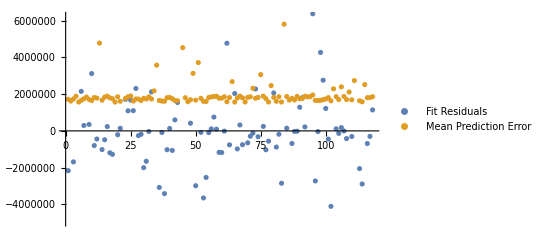

```mathematica
(* 针对模型进行可视化误差分析，原始数据与拟合模型之间的拟合优度 *)
ListPlot[
	{model["FitResiduals"],model["MeanPredictionErrors"]},
	PlotLegends->Placed[{"Fit Residuals","Mean Prediction Error"},Top]
]
```

```mathematica
(* 生成随机数字 *)
SeedRandom["CKM"];
RandomReal[]
```

0.0229577

```mathematica
RandomInteger[]
```

0

```mathematica
RandomInteger[5]
```

2

```mathematica
RandomInteger[5]
```

5

```mathematica
RandomReal[{3,5}]
```

4.70974

```mathematica
RandomInteger[{3,5}]
```

5

```mathematica
RandomReal[{1,6},10]
```

{4.22389,5.08674,2.28061,1.45062,2.76,3.40397,4.23413,2.60935,1.76748,5.28506}

```mathematica
RandomInteger[{0,10},{3,5}]
```

{{6,7,8,10,5},{10,7,9,9,4},{9,3,3,3,1}}

```mathematica
MatrixForm[{
RandomReal[{0,1},4],
RandomReal[{1,2},4],
RandomReal[{2,3},4]
}]
```

(0.762866 | 0.774061 | 0.304006 | 0.544943
1.78507 | 1.0696 | 1.59658 | 1.18917
2.81896 | 2.91632 | 2.04597 | 2.07517)

```mathematica
vals = Range[5]
```

{1,2,3,4,5}

```mathematica
(* 随机采样 *)
RandomChoice[vals,3]
```

{3,4,2}

```mathematica
RandomChoice[vals,3]
```

{3,2,5}

```mathematica
(* RandomChoice是可替换采样，允许抽取多于本身列表长度 *)
RandomChoice[vals,30]
```

{5,2,3,3,5,3,2,5,2,5,3,5,4,4,1,3,5,3,2,3,2,2,4,3,4,5,3,4,1,4}

```mathematica
(* RandomSample是无替换采样，不允许抽取多与本身长度的数据 *)
RandomSample[vals,1]
```

{1}

```mathematica
vals = Table[
	N[
Mean[RandomChoice[Range[100],5]]
],{i,1,10,1}
]
```

{61.,53.,54.,47.8,68.6,51.6,55.2,24.8,46.8,59.}

```mathematica
Mean[vals]
```

52.18

```mathematica
Clear[popSelect,LargeCountriesCellAndInternet,largeCountry,fit1,fit2,fit3,fit4,model,vals]
```